```mathematica
g=GridGraph[{3,3,3}, VertexLabels->Table[i->Subscript[v,i],{i,27}]];
```

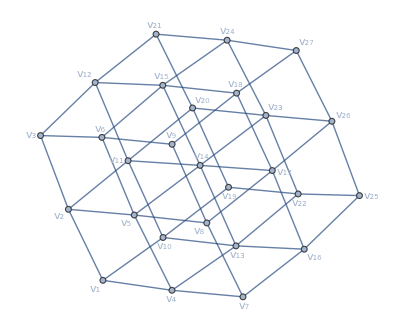

```mathematica
g
```

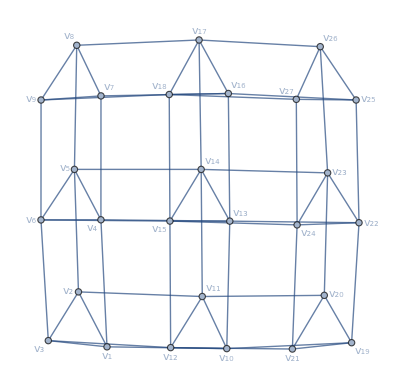

```mathematica
g =EdgeAdd[g, {1<->3,4<->6, 7<->9, 10<->12, 13<->15, 16<->18, 19<->21, 22<->24, 25<->27}]
```

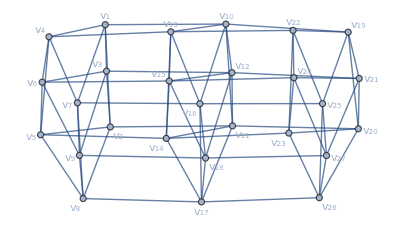

```mathematica
g=EdgeAdd[g, {1<->7, 2<->8, 3<->9, 10<->16, 11<->17, 12<->18, 19<->25, 20<->26, 21<->27}]
```

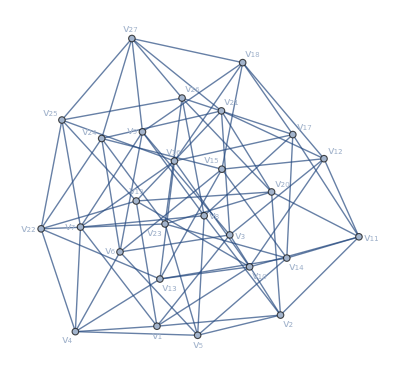

```mathematica
g=EdgeAdd[g, {1<->19, 2<->20, 3<->21, 4<->22, 5<->23, 6<->24, 7<->25, 8<->26, 9<->27}]
```

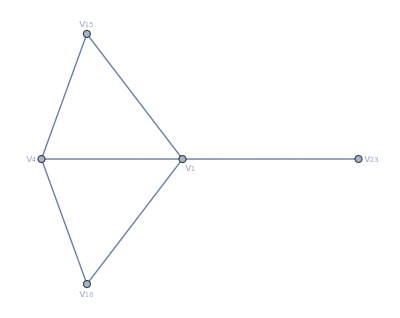

```mathematica
VertexContract[g, {{1,2}, {1,10}, {1,11}, {4,13}, {8,17}, {16,25}, {27,9}, {8,18}, {27,7}, {27,3}, {8,12}, { 27,21}, {5,6}, {19,20}, {19,22}, {5,8}, {19,1}, {26,19}, {26,27}, {5,14}, {24,5}, {24,26}}]
```